```mathematica
Needs["MFGraphs`"]
```

```mathematica
Get["/Users/ribeirrd/Dropbox/My Mac (kl-14835.kaust.edu.sa)/Documents/workspace/MFGraphs/MFGraphs/MFGraphs.m"](*Ricardo, use this when not running from eclipse.*)
```

```mathematica
Names["MFGraphs`*"]
```

{A,alpha,AtHead,AtTail,A$,beta,DataG,DataToEquations,EqEliminatorX,F,FixedPointSolverStepX,FixedSolverStepX2,g,g$2733,H,I1,I2,Intg,m,m$,n,OtherWay,p,Parameters,p$,S1,S10,S11,S12,S13,S14,S15,S16,S2,S3,S4,S5,S6,S7,S8,S9,StartSolverX,Test,TransitionsAt,triple2path,U1,U2,V,V$2733,W,W$2733,x,x$}

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[24];
MFGEquations=DataToEquations[Data];
```

DataToEquations: Finished assembling strucural equations:

DataToEquations: Critical case ...

DataToEquations: Reducing ...

EqEliminatorX: Reached a solution!

DataToEquations: Done.

#### Non-linear case

```mathematica
MFGEquations["EqGeneralCase"]
```

1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

```mathematica
MFGEquations["reduced"]
```

{NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-u232+u237]&&NonNegative[u237-u239]&&NonNegative[u232-u237]&&NonNegative[u232-u239]&&NonNegative[-u237+u239]&&NonNegative[-u232+u239]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-u232+u237==0)&&(jt223==0||u237-u239==0)&&(jt223==0||u232-u237==0)&&(-jt223==0||u232-u239==0)&&(-jt223==0||-u237+u239==0)&&(2+jt223==0||-u232+u239==0),<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1|>}

```mathematica
KeySort[MFGEquations["criticalreduced"][[2]]]//Simplify
```

<|j207→1,j208→3,j209→2,j210→3,j211→1,j212→2,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-0,jt222→0,jt223→0,jt224→-0,jt225→-0,jt226→2+0,jt227→0,jt228→2,jt229→3,jt230→0,u231→5,u232→4,u233→6,u234→1,u235→5,u236→6,u237→-1+5,u238→1,u239→-2+6,u240→1,u241→5,u242→6|>

```mathematica
MFGEquations["criticalreduced"][[2]]/.MFGEquations["criticalreduced"][[2]]//KeySort
```

<|j207→1,j208→3,j209→2,j210→3,j211→1,j212→2,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-0,jt222→0,jt223→0,jt224→-0,jt225→-0,jt226→2+0,jt227→0,jt228→2,jt229→3,jt230→0,u231→5,u232→4,u233→6,u234→1,u235→5,u236→6,u237→-1+5,u238→1,u239→-2+6,u240→1,u241→5,u242→6|>

```mathematica
FixedSolverStepX2[MFGEquations][MFGEquations["criticalreduced"][[2]]
]
```

Step: nonlinear: 1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: SYSTEM: NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-u232+u237]&&NonNegative[u237-u239]&&NonNegative[u232-u237]&&NonNegative[u232-u239]&&NonNegative[-u237+u239]&&NonNegative[-u232+u239]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-u232+u237==0)&&(jt223==0||u237-u239==0)&&(jt223==0||u232-u237==0)&&(-jt223==0||u232-u239==0)&&(-jt223==0||-u237+u239==0)&&(2+jt223==0||-u232+u239==0)&&1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: newsolve 2: {NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-4.23373+1. u231]&&NonNegative[0.601571+1. u231-1. u233]&&NonNegative[4.23373-1. u231]&&NonNegative[4.8353-1. u233]&&NonNegative[-0.601571-1. u231+1. u233]&&NonNegative[-4.8353+1. u233]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-4.23373+1. u231==0)&&(jt223==0||0.601571+1. u231-1. u233==0)&&(jt223==0||4.23373-1. u231==0)&&(-jt223==0||4.8353-1. u233==0)&&(-jt223==0||-0.601571-1. u231+1. u233==0)&&(2+jt223==0||-4.8353+1. u233==0),<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Step: Reducing ...

Step: newsolve 2 resolved{False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Something is wrong with the equations: False

Step: newsolve 3: {False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>

```mathematica
MFGEquations["EqGeneralCase"]/.%
```

True

```mathematica
FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced"][[2]],10]
```

Step: nonlinear: 1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: SYSTEM: NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-u232+u237]&&NonNegative[u237-u239]&&NonNegative[u232-u237]&&NonNegative[u232-u239]&&NonNegative[-u237+u239]&&NonNegative[-u232+u239]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-u232+u237==0)&&(jt223==0||u237-u239==0)&&(jt223==0||u232-u237==0)&&(-jt223==0||u232-u239==0)&&(-jt223==0||-u237+u239==0)&&(2+jt223==0||-u232+u239==0)&&1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: newsolve 2: {NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-4.23373+1. u231]&&NonNegative[0.601571+1. u231-1. u233]&&NonNegative[4.23373-1. u231]&&NonNegative[4.8353-1. u233]&&NonNegative[-0.601571-1. u231+1. u233]&&NonNegative[-4.8353+1. u233]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-4.23373+1. u231==0)&&(jt223==0||0.601571+1. u231-1. u233==0)&&(jt223==0||4.23373-1. u231==0)&&(-jt223==0||4.8353-1. u233==0)&&(-jt223==0||-0.601571-1. u231+1. u233==0)&&(2+jt223==0||-4.8353+1. u233==0),<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Step: Reducing ...

Step: newsolve 2 resolved{False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Something is wrong with the equations: False

Step: newsolve 3: {False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Step: nonlinear: 1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: SYSTEM: NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-u232+u237]&&NonNegative[u237-u239]&&NonNegative[u232-u237]&&NonNegative[u232-u239]&&NonNegative[-u237+u239]&&NonNegative[-u232+u239]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-u232+u237==0)&&(jt223==0||u237-u239==0)&&(jt223==0||u232-u237==0)&&(-jt223==0||u232-u239==0)&&(-jt223==0||-u237+u239==0)&&(2+jt223==0||-u232+u239==0)&&1-u231+u237==-0.073805&&4-u232==0.840074&&2-u233+u239==0.324624

Step: newsolve 2: {NonNegative[1-jt223]&&NonNegative[jt223]&&NonNegative[jt223]&&NonNegative[-jt223]&&NonNegative[-jt223]&&NonNegative[2+jt223]&&NonNegative[-4.23373+1. u231]&&NonNegative[0.601571+1. u231-1. u233]&&NonNegative[4.23373-1. u231]&&NonNegative[4.8353-1. u233]&&NonNegative[-0.601571-1. u231+1. u233]&&NonNegative[-4.8353+1. u233]&&(1-jt223==0||jt223==0)&&(jt223==0||-jt223==0)&&(-jt223==0||2+jt223==0)&&(1-jt223==0||-4.23373+1. u231==0)&&(jt223==0||0.601571+1. u231-1. u233==0)&&(jt223==0||4.23373-1. u231==0)&&(-jt223==0||4.8353-1. u233==0)&&(-jt223==0||-0.601571-1. u231+1. u233==0)&&(2+jt223==0||-4.8353+1. u233==0),<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Step: Reducing ...

Step: newsolve 2 resolved{False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

Something is wrong with the equations: False

Step: newsolve 3: {False,<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>}

<|j211→1,j212→2,u240→1,j207→1,j208→3,j209→2,j210→3,j213→0,j214→0,j215→0,j216→0,j217→0,j218→0,jt219→0,jt220→1,jt221→1-jt223,jt222→jt223,jt224→-jt223,jt225→-jt223,jt226→2+jt223,jt227→0,jt228→2,jt229→3,jt230→0,u234→1,u241→u231,u242→u233,u235→u231,u236→u233,u238→1,u232→3.15993,u237→-1.0738+1. u231,u239→-1.67538+1. u233|>

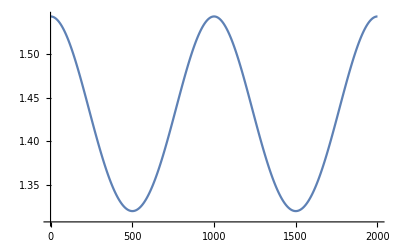

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.